```mathematica
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
DiskBlend[colorA_,colorB_]:=Graphics[
Table[{
Blend[
{
colorA,
colorB
}
,x],Disk[{0,.5x},.1]}
,{x,0,1,1/10}]]
HEXtoRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

{RGBColor[0.5176470588235293, 0.4, 1.],RGBColor[1., 0.4, 0.4],RGBColor[0.4588235294117647, 1., 0.4],RGBColor[1., 0.4, 0.9607843137254902],RGBColor[1., 0.9803921568627451, 0.45098039215686275]}

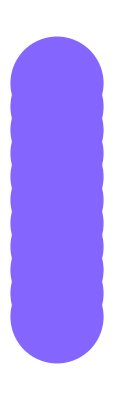
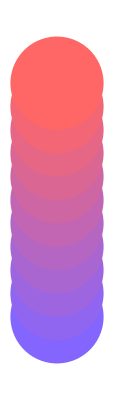
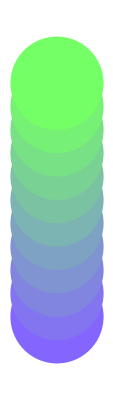
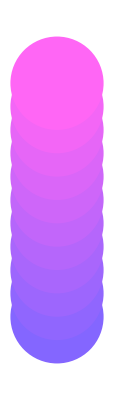
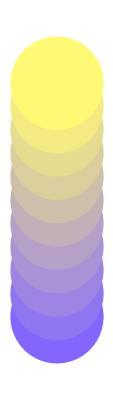
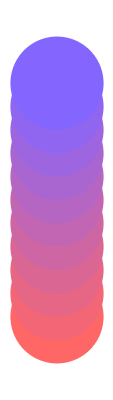
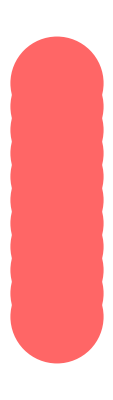
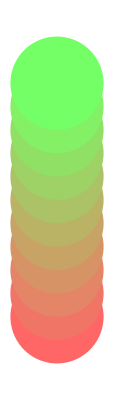
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*Define Color Palette*)
hexColors={"#8466FF","#FF6666","#75FF66","#FF66F5","#FFFA73"};
(*Convert color spaces*)
rgbColors=HEXtoRGB/@hexColors
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
(*Blend*)
colorTuples=Tuples[rgbColors,2];
blends=DiskBlend[#[[1]],#[[2]]]&/@colorTuples;
Partition[blends,Ceiling[Length[blends]]]//Grid
```